```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts"]
```

C:\Users\pglpm\repositories\genobayes\scripts

```mathematica
datacf=T[Import["condcounts_sA.csv"][[2;;,2;;]]];
```

```mathematica
Dimensions[datacf]
```

{2,188}

```mathematica
datacf[[;;,1;;3]]
```

{{3323,1045,1958},{1214,447,740}}

```mathematica
datacf[[;;,1;;3]]+{10^5,2*10^5}
```

{{103323,101045,101958},{201214,200447,200740}}

```mathematica
Total@%
```

{304537,301492,302698}

```mathematica
logprob[t_,g_]:=Block[{r2=datacf[[;;,{2*g-1,2*g}]]+t},
Total@Flatten@LogGamma[r2]-
Total@LogGamma[Total@r2]+
(Length@T@r2)*(LogGamma[Total@t]-Total@LogGamma[t])]
```

```mathematica
logprob[{11,20},3]//N
```

-3570.92

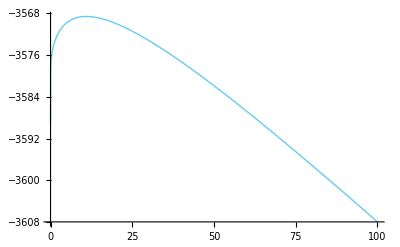

```mathematica
Plot[logprob[{x,10},1],{x,0,100}]
```

```mathematica
xy=FindMaximum[{logprob[{x,y},2],x>0,y>0},{{x,0.1},{y,0.1}}]
```

{-3549.04,{x→45866.2,y→17441.3}}

```mathematica
Total@Flatten@datacf[[;;,{1,2}]]
```

6029

```mathematica
bd[x_,a_,b_]=PDF[BetaDistribution[b,a],x]
```

Piecewise[{{((1-x)^(-1+a) x^(-1+b))/Beta[b,a], 0<x<1}, {0, True}}]

```mathematica
oldtheta[g_,i_]:=datacf[[;;,2*g-1+i]];
newtheta[g_,i_]:=datacf[[;;,2*g-1+i]]+({x,y}/.FindMaximum[{logprob[{x,y},g],x>0,y>0},{{x,1},{y,1}}][[2]])
```

```mathematica
checkgenes=94;
```

```mathematica
checkdata=Flatten[Table[
theta=newtheta[gx,ax];tot=Total@theta;
{theta[[2]]/tot,Sqrt[(Times@@theta)/(tot^2*(1+tot))]},{gx,1,checkgenes},{ax,0,1}],1];
```

```mathematica
checkgenes=94;geneseq=Import["allcondfreqs_1gene_thetamax_sA.csv"][[1,2;;checkgenes*2+1]];
symptomnames={"A","B","C"};allelenames={"A","B"};
```

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
Do[Print[sym];
datacf=T[Import["condcounts_s"<>sym<>".csv"][[2;;,2;;]]];
ClearAll[logprob,newtheta];
logprob[t_,g_]:=Block[{r2=datacf[[;;,{2*g-1,2*g}]]+t},
Total@Flatten@LogGamma[r2]-
Total@LogGamma[Total@r2]+
(Length@T@r2)*(LogGamma[Total@t]-Total@LogGamma[t])];

newtheta[g_,i_]:=datacf[[;;,2*g-1+i]]+({x,y}/.FindMaximum[{logprob[{x,y},g],x>0,y>0},{{x,1},{y,1}}][[2]]);

checkdata=Flatten[Table[
theta=newtheta[gx,ax];tot=Total@theta;
{theta[[2]]/tot,Sqrt[(Times@@theta)/(tot^2*(1+tot))]},{gx,1,checkgenes},{ax,0,1}],1];

min=Min[checkdata[[;;,1]]-checkdata[[;;,2]]];
max=Max[checkdata[[;;,1]]+checkdata[[;;,2]]];plot=ErrorListPlot[checkdata[[;;,{1,2}]],PlotRange->{min,max},Joined->False,AspectRatio->1/6,Frame->Auto,Axes->None,FrameLabel->{Style[gene,41],Style[freq[symptom|"gene allele"],41]},
FrameStyle->Directive[Large],
FrameTicks->{Auto,{T@{Range[checkgenes*2],Style[#,15]&/@(Rotate[#,Pi/2]&/@(geneseq))},None}},
PlotStyle->PointSize[Scaled[0.005]],GridLines->{Range[1/2,checkgenes*2+1/2,2],Auto},ImageSize->a4longside*{6,1},Epilog->Text[Style["symptom "<>sym,42],Sequence@@labelposition[{0.5,0.9}]]];
Export["mathematica_check"<>sym<>".pdf",plot];,
{sym,symptomnames}]
```

```mathematica
(* with quantiles instead of std *)
Do[Print[sym];
datacf=T[Import["condcounts_s"<>sym<>".csv"][[2;;,2;;]]];
ClearAll[logprob,newtheta];
logprob[t_,g_]:=Block[{r2=datacf[[;;,{2*g-1,2*g}]]+t},
Total@Flatten@LogGamma[r2]-
Total@LogGamma[Total@r2]+
(Length@T@r2)*(LogGamma[Total@t]-Total@LogGamma[t])];

newtheta[g_,i_]:=datacf[[;;,2*g-1+i]]+({x,y}/.FindMaximum[{logprob[{x,y},g],x>0,y>0},{{x,1},{y,1}}][[2]]);

checkdata=Flatten[Table[
theta=newtheta[gx,ax];tot=Total@theta;
{{gx*2-1+ax,theta[[2]]/tot},
ErrorBar[-theta[[2]]/tot+Quantile[BetaDistribution[theta[[2]],theta[[1]]],{0.05,0.95}]]},{gx,1,checkgenes},{ax,0,1}],1];

min=Min[checkdata[[;;,1,2]]+checkdata[[;;,2,1,1]]];
max=Max[checkdata[[;;,1,2]]+checkdata[[;;,2,1,2]]];plot=ErrorListPlot[checkdata[[;;,{1,2}]],PlotRange->{min,max},Joined->False,AspectRatio->1/6,Frame->Auto,Axes->None,FrameLabel->{Style[gene,41],Style[freq[symptom|"gene allele"],41]},
FrameStyle->Directive[Large],
FrameTicks->{Auto,{T@{Range[checkgenes*2],Style[#,15]&/@(Rotate[#,Pi/2]&/@(geneseq))},None}},
PlotStyle->PointSize[Scaled[0.005]],GridLines->{Range[1/2,checkgenes*2+1/2,2],Auto},ImageSize->a4longside*{6,1},Epilog->Text[Style["symptom "<>sym,42],Sequence@@labelposition[{0.5,0.9}]]];
Export["mathematica_05quantile_s"<>sym<>".pdf",plot];,
{sym,symptomnames}]
```

```mathematica
a
```

a

```mathematica
oldtheta[3,1]
```

{1660,601}

```mathematica
newtheta[3,1]
```

{88092.5,33460.2}

```mathematica
bd[0.5,Sequence@@(newtheta[3,0])]
```

4.036684122×10^-5576

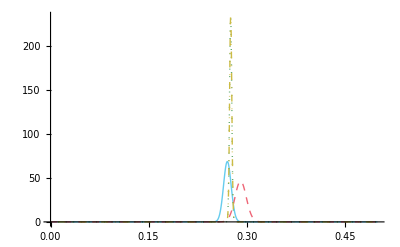

```mathematica
Plot[{bd[x,Sequence@@newtheta[1,0]],bd[x,Sequence@@newtheta[1,1]],bd[x,Sequence@@newtheta[2,0]],bd[x,Sequence@@newtheta[2,1]]},{x,0,0.5},PlotRange->All]
```